```mathematica
d1:=0.4;
d2:=0.1;
m1:=0.35;
```

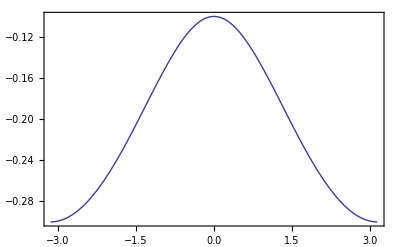

```mathematica
f3[z_]:=m1-√(d1^2+d2^2-2*d1*d2*Cos[z])
Plot[{f3[z]},{z,-Pi,Pi},Frame->True]
```

```mathematica
Integrate[HeavisideTheta[en^2-(mass-√(dl1^2+dl2^2-2*dl1*dl2*Cos[z]))^2], {z,0,Pi}, Assumptions-> {dl1>dl2, mass>dl1-dl2, mass<dl1+dl2, en>0}]
```

1/2 π (1+1/Sign[en^2-(dl1+dl2-mass)^2])

1/2 π (1+1/Sign[en^2-(dl1+dl2-mass)^2])

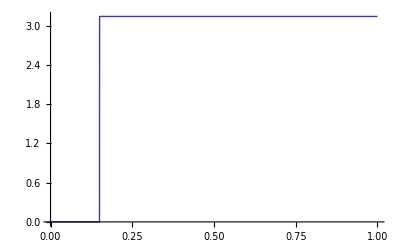

```mathematica
1/2 π (1+1/Sign[en^2-(dl1+dl2-mass)^2])
Plot[1/2 π (1+1/Sign[e^2-(d1+d2-m1)^2]), {e,0,1}]
```

```mathematica
Manipulate[Plot[HeavisideTheta[en^2-(m1-√(d1^2+d2^2-2*d1*d2*Cos[z]))^2], {z,0,Pi}],{en, 0, 1}]
```

```mathematica
(d1+d2)-m1
```

0.15